```mathematica
The angle difference between two driven damped pendulums, with driven force is 0.5 N, and initial angle difference is 0.001.
```

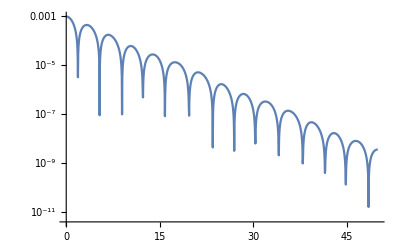

```mathematica
length = 9.8;
grav = 9.8;
dt = 0.04;
ts = 0.0; tend = 50;
tL = Range[ts, tend, dt];
lt = Length[tL];
theta = 0 tL;
theta2 = 0 tL;
omega = 0 tL;
theta[[1]] = 0.2;
theta2[[1]] = 0.201;
omega[[1]] = 0.0;
const = grav/length;
damp = 1/2;
drivenforce=0.5;
drivenfreq=2/3;
Do[omega[[i]] = omega[[i-1]]-dt*(Sin[theta[[i-1]]]* const+damp omega[[i-1]]-drivenforce*Sin[drivenfreq*tL[[i-1]]]);
theta[[i]] = theta[[i-1]]+omega[[i]] dt;
,{i,2,lt}];
Do[omega[[i]] = omega[[i-1]]-dt*(Sin[theta2[[i-1]]]* const+damp omega[[i-1]]-drivenforce*Sin[drivenfreq*tL[[i-1]]]);
theta2[[i]] = theta2[[i-1]]+omega[[i]] dt;
,{i,2,lt}];

(*tth = Table[{tL[[j]],theta[[j]]},{j,lt}];*)
tth1 = Table[{tL[[j]],Abs[theta[[j]]-theta2[[j]]]},{j,lt}];
ListLogPlot[tth1, PlotRange->All, Joined->True]
```

As we see the angle difference between the two pendulums decrease with time, and the two pendulums eventually have the same dynamics at the end.

The angle difference between two driven damped pendulums, with driven force is 1.2 N, and initial angle difference is 0.001.

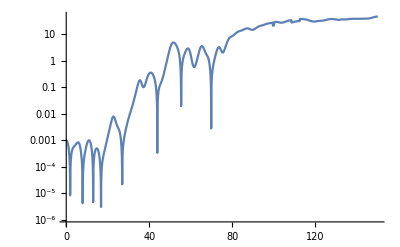

```mathematica
ClearAll["Global`*"] 
length = 9.8;
grav = 9.8;
dt = 0.04;
ts = 0.0; tend = 150;
tL = Range[ts, tend, dt];
lt = Length[tL];
theta = 0 tL;
theta2 = 0 tL;
omega = 0 tL;
theta[[1]] = 0.250;
theta2[[1]] = 0.251;
omega[[1]] = 0.0;
const = grav/length;
damp = 1/2;
drivenforce=1.2;
drivenfreq=2/3;
Do[omega[[i]] = omega[[i-1]]-dt*(Sin[theta[[i-1]]]* const+damp omega[[i-1]]-drivenforce*Sin[drivenfreq*tL[[i-1]]]);
theta[[i]] = theta[[i-1]]+omega[[i]] dt;
,{i,2,lt}];
Do[omega[[i]] = omega[[i-1]]-dt*(Sin[theta2[[i-1]]]* const+damp omega[[i-1]]-drivenforce*Sin[drivenfreq*tL[[i-1]]]);
theta2[[i]] = theta2[[i-1]]+omega[[i]] dt;
,{i,2,lt}];

Do[If[theta[[i]]>Pi,theta[[i]]=theta[[i]]-2 Pi];
If[theta[[i]]<-Pi,theta[[i]]=theta[[i]]+2 Pi],{i,lt}]
Do[If[theta2[[i]]>Pi,theta2[[i]]=theta2[[i]]-2 Pi];
If[theta2[[i]]<-Pi,theta2[[i]]=theta2[[i]]+2 Pi],{i,lt}]

theta;
(*tth = Table[{tL[[j]],theta[[j]]},{j,lt}];*)
tth = Table[{tL[[j]],Abs[theta[[j]]-theta2[[j]]]},{j,lt}];
ListLogPlot[tth, PlotRange->All, Joined->True]
```

As we see the difference in the angle between the two pendulums keep increasing and eventually they have total different dynamics.